```mathematica
distribution:=EmpiricalDistribution[{{2,3,4,5,6,7,8,9,10,11,12},{1/36,2/36,3/26,4/36,5/36,6/36,5/36,4/36,3/36,2/36,1/36}}]
```

```mathematica
cumulative:=CDF[distribution]
```

```mathematica
Dist
```

```mathematica
DataDistribution[{{2,3,4,5,6,7,8,9,10,11,12},{1/36,2/36,3/26,4/36,5/36,6/36,5/36,4/36,3/36,2/36,1/36}}]
```

DataDistribution[{{2,3,4,5,6,7,8,9,10,11,12},{1/36,1/18,3/26,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36}}]

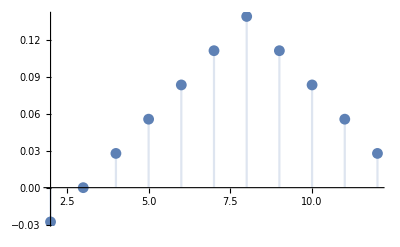

```mathematica
DiscretePlot[(5-Abs[x-8])/36,{x,2,12}]
```

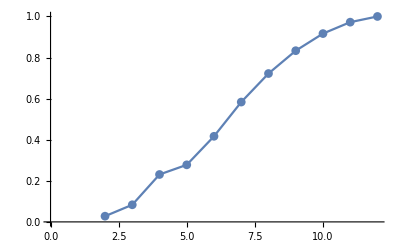

```mathematica
ListLinePlot[{{2,1/36},{3,1/12},{4,3/13},{5,5/18},{6,5/12},{7,7/12},{8,13/18},{9,5/6},{10,11/12},{11,35/36},{12,1}},PlotMarkers->Automatic]
```

```mathematica
DiscretePlot[x,{x,{}}]
```

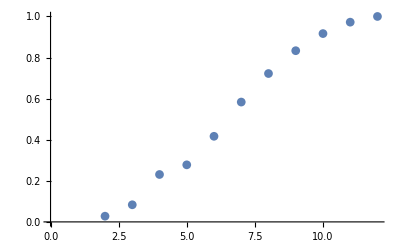

```mathematica
ListPlot[{{2,1/36},{3,1/12},{4,3/13},{5,5/18},{6,5/12},{7,7/12},{8,13/18},{9,5/6},{10,11/12},{11,35/36},{12,1}},PlotMarkers->Automatic]
```

```mathematica
DiscretePlot[{{2,1/36},{3,1/12},{4,3/13},{5,5/18},{6,5/12},{7,7/12},{8,13/18},{9,5/6},{10,11/12},{11,35/36},{12,1}},PlotMarkers->Automatic]
```

DiscretePlot::argr: DiscretePlot called with 1 argument; 2 arguments are expected.

DiscretePlot[{{2,1/36},{3,1/12},{4,3/13},{5,5/18},{6,5/12},{7,7/12},{8,13/18},{9,5/6},{10,11/12},{11,35/36},{12,1}},PlotMarkers→Automatic]

```mathematica
array:={1/36,1/12,3/13,5/18,5/12,7/12,13/18,5/6,11/12,35/36,1}
```

```mathematica
f[x_]:=Part[array,x-1]
```

```mathematica
f[2]
```

1/36

```mathematica
1/36
f[3]
```

1/36

1/12

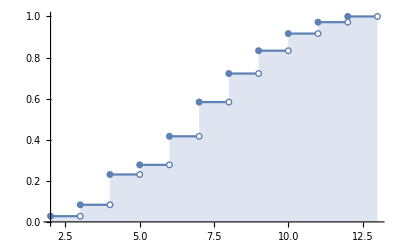

```mathematica
DiscretePlot[f[n],{n,2,12},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"}]
```